# Local Optimization on the Gaussian manifold

This notebook is intended as a guide to using the optimization algorithm performing gradient descent over the manifold of pure bosonic or fermionic Gaussian states.

```mathematica
Quit[];
```

# The GaussianOptimization.m package and its functions

```mathematica
SetDirectory[NotebookDirectory[]];
<<GaussianOptimization`
```

```mathematica
$GOFunctions
```

{GOapproxExp,GOConditionalLog,GOConstructPurificationBos,GOConstructPurificationFerm,GOExtractStdForm,GOinvMSp,GOlogfunction,GOMranO,GOMranSp,GOOBasis,GOOptimize,GOSpBasis,GOSpBasisNoU1,GOSpBasisNoUN,GOTransform,GOTransformtoJ,GOΩqpqp,GOΩqqpp}

## Optimization algorithm

```mathematica
?GOOptimize
```

Optimization of a scalar function over the manifold of Gaussian states. 

The algorithm initializes at at various specified starting points in the manifold, each of which defines a trajectory for the optimization. 
At each multiple of 5 steps, the algorithm retains only the 20% of the trajectories with the lowest function values and highest gradient norm, 
respectively. The optimization is terminated when the final remaining trajectory (or trajectories) first satisfies one of three stopping criteria: 
a lower bound on the gradient norm, a limit on the number of iterations, and a relative difference in function value below 10^-10. 

Input arguments are: 
(1) function to be optimised f[ M, J0] 
(2) associated gradient function df[ M, J0, Kbasis] 
(3) initial J 
(4) list of initial transformations {M1,M2,...} 
(5) specification of basis types for subsystems A and B { 'basisA', 'basisB'} (must be strings and must specify 'None' if no optimization occurs in one subsystem) 
(6) no. of degrees of freedom in subsystems { dimA, dimB} (must specify dimB=0 and basisB='None' if there is no splitting into subsystems) 
(7) tolerance on norm of gradient as stopping criterion
(8) iteration limit as stopping criterion (default=infinity)

Output arguments are: 
(1) final function value
(2) final transformation M 
(3) list of the no. of corrections of the step size per iteration 
(4) list of the function values for the final surviving trajectory 
(5) list of the values of the gradient norm for the final surviving trajectory 
(6) Natural \!\(\*
StyleBox["metric",
FontWeight->"Plain"]\)\!\(\*
StyleBox[" ",
FontWeight->"Plain"]\)\!\(\*
StyleBox["on",
FontWeight->"Plain"]\)\!\(\*
StyleBox[" ",
FontWeight->"Plain"]\)\!\(\*
StyleBox["the",
FontWeight->"Plain"]\)\!\(\*
StyleBox[" ",
FontWeight->"Plain"]\)\!\(\*
StyleBox["manifold",
FontWeight->"Plain"]\)\!\(\*
StyleBox[" ",
FontWeight->"Plain"]\)

## Fundamental definitions and basic tools

Symplectic forms and various matrices

```mathematica
?GOΩqqpp
```

GOΩqqpp[ N] generates the symplectic form in basis (q1,q2,...,p1,p2,...) for N bosonic deg. of freedom

```mathematica
?GOΩqpqp
```

GOΩqpqp[ N] generates the symplectic form in basis (q1,p1,q2,p2,...) for N bosonic deg. of freedom

```mathematica
?GOTransformtoJ
```

GOTransformtoJ[ G] generates the complex structure associated with a cov. matrix G by computing J=-G.Ω

```mathematica
?GOTransform
```

GOTransform[ N] generates a N-dim. basis transformation matrix (q1,p1,q2,p2,...)→(q1,q2,...,p1,p2,...)

```mathematica
?GOMranSp
```

MranSp[ N] generates a random NxN symplectic matrix

```mathematica
?GOMranO
```

MranO[ N] generates a random NxN orthogonal matrix

Lie algebra bases

```mathematica
?GOSpBasis
```

SpBasis[ N] generates sp(2N,R) Lie algebra basis

```mathematica
?GOSpBasisNoUN
```

spBasisNoUN[ N] generates sp(2N,R)/U(N) Lie algebra basis

```mathematica
?GOSpBasisNoU1
```

spBasisNoU1[ N] generates sp(2N,R)/U(1)^N Lie algebra basis

```mathematica
?GOOBasis
```

OBasis[ N] generates o(2N,R) Lie algebra basis

Purifications and the standard form

```mathematica
?GOExtractStdForm
```

GOExtractStdForm[ G] returns the parameters for constructing the standard form of G (list of the r_i and the transformation matrix that puts G into standard form)

```mathematica
?GOConstructPurificationBos
```

GOConstructPurificationBos[ rlist, { dimA, dimB}] generates the complex structure for the (dimA+dimB)-dimensional purification of a dimA-dimensional bosonic Gaussian state in standard form

```mathematica
?GOConstructPurificationFerm
```

GOConstructPurificationBos[ rlist, { dimA, dimB}] generates the complex structure for the (dimA+dimB)-dimensional purification of a dimA-dimensional fermionic Gaussian state in standard form

Tools for computational efficiency

```mathematica
?GOapproxExp
```

approxExp[ ϵ, K]=(1 + ϵ/2 K)/(1 - ϵ/2 K) approximates MatrixExponential[ϵX]

```mathematica
?GOlogfunction
```

logfunction[ x] takes value 0 when x=0 and log[x] otherwise

```mathematica
?GOConditionalLog
```

GOConditionalLog[ x] calculates MatrixLog[ x] by applying logfunction to the eigenvalues of x

```mathematica
?GOinvMSp
```

invMSp[ m] inverts a symplectic matrix m as m^-1=-ΩmΩ

## Applications implemented in GaussianOptimization.m

```mathematica
$GOApplicationsFunctions
```

{GOEoPBos,GOEoPFerm,GOEoPgradBos,GOEoPgradFerm,GORestrictionAA}

Entanglement of Purification

```mathematica
?GORestrictionAA
```

GORestrictionAA[ {dimA1, dimB1, dimA2, dimB2}] generates the restriction function for use in calculating EoP for a system decomposed into degrees of freedom {dimA1, dimB1, dimA2, dimB2}

```mathematica
?GOEoPBos
```

GOEoPBos[ Restriction] generates a function f[ M, J_0] which calculates the bosonic EoP for the given restriction

```mathematica
?GOEoPgradBos
```

GOEoPgradBos[ Restriction] generates a function df[ M, J_0, K] which calculates the gradient of the bosonic EoP for the given restriction with respect to the Lie algebra basis K

```mathematica
?GOEoPFerm
```

GOEoPBos[ Restriction] generates a function f[ M, J_0] which calculates the fermionic EoP for the given restriction

```mathematica
?GOEoPgradFerm
```

GOEoPgradFerm[ Restriction] generates a function df[ M, J_0, K] which calculates the gradient of the fermionic EoP for the given restriction with respect to the Lie algebra basis K

Complexity of Purification

```mathematica
?GOCoPBos
```

GOCoPBos[ J_T] generates a function f[ M, J_R] which calculates the bosonic CoP with respect to the given target state J_T

```mathematica
?GOCoPgradBos
```

GOCoPBos[ J_T] generates a function df[ M, J_R, K] which calculates the gradient of the bosonic CoP with respect to the given target state J_T and the Lie algebra basis K

Energy of quadratic Hamiltonians

```mathematica
?GOenergyBos
```

GOenergyBos[ h] generates an energy function f[ M, J_0] for a bosonic quadratic Hamiltonian H=h_abξ^aξ^b

```mathematica
?GOenergygradBos
```

GOenergygradBos[ h] generates an energy gradient function df[ M, J_0, K] for a bosonic quadratic Hamiltonian H=h_abξ^aξ^b with respect to the Lie algebra basis K

```mathematica
?GOenergyFerm
```

GOenergyFerm[ h] generates an energy function f[ M, J_0] for a fermionic quadratic Hamiltonian H=h_abξ^aξ^b

```mathematica
?GOenergygradFerm
```

GOenergygradBos[ h] generates an energy gradient function df[ M, J_0, K] for a fermionic quadratic Hamiltonian H=h_abξ^aξ^b with respect to the Lie algebra basis K

# Selected examples of applications

Bosonic Entanglement of Purification (EoP)

#### Preliminary definitions: Functions to generate the initial covariance matrices for a lattice free scalar field theory

```mathematica
FourierMatrixElement[N_]:=Function[{k,x},Exp[I 2 Pi x k /N]/Sqrt[N]];
DispersionRelation[m_,N_,l_]:=Function[{k},Sqrt[m^2+4/l^2  (Sin[Pi k/N])^2]];
```

```mathematica
FT[n_]:=Module[{f,pos,val},
f=FourierMatrixElement[n];
pos=Table[{x,k},{k,n},{x,n}]//Flatten[#,1]&;
val=Table[f[k,x]//N,{k,n},{x,n}]//Flatten[#,1]&;
SparseArray[pos->val]];
```

```mathematica
Diag[m_,n_,l_]:=Module[{ω},
ω=DispersionRelation[m,n,l];
DiagonalMatrix[Table[ω[k],{k,n}]]];
```

```mathematica
invDiag[m_,n_,l_]:=Module[{ω},
ω=DispersionRelation[m,n,l];
DiagonalMatrix[Table[1/ω[k],{k,n}]]];
```

```mathematica
CM[N_,m_,l_]:=Module[{F,D,invD,G,Tr},
F=FT[N];D=Diag[m,N,l]; invD=invDiag[m,N,l];
G=ArrayFlatten[({{F.D.ConjugateTranspose[F], 0}, {0, F.invD.ConjugateTranspose[F]}})]//Chop//SparseArray];
```

```mathematica
partialCM[N_,m_,l_,d_,dim1_,dim2_]:=
Module[{dim, halfdim, bigCM, indices1, indices2,indices, partialCM, Tr},

bigCM=CM[N,m,l];
dim=Length[bigCM]; halfdim=dim/2;

indices1=Thread[{Table[x,{x,dim1}],Table[x+halfdim,{x,dim1}]}]//Flatten[#,1]&;
indices2=Thread[{Table[dim1+d+x,{x,dim2}],Table[dim1+d+x+halfdim,{x,dim2}]}]//Flatten[#,1]&;

indices=Join[indices1,indices2];

partialCM=bigCM[[indices,indices]]];
```

#### Example of the setup and execution for a typical optimization

1. Generate the initial mixed state covariance matrix

Note: The functions used to define the initial mixed state covariance matrix below are beyond the scope of the GaussianOptimization.m package and are not included in it.
In the example below, the mixed state is obtained for a system with total number of lattice sites 100 with 3 sites per subsystem in the initial system, mass term 0.1, lattice spacing 1, 
and no lattice sites separating the subsystems.

```mathematica
CM0=partialCM[100,.1,1,0,3,3];
```

2. Generate the purified state complex structure (in this case for a minimal purification)

```mathematica
{rlist,MTra}=GOExtractStdForm[CM0];
J0=GOConstructPurificationBos[rlist,{6,6}];
```

3. Generate a list of the starting points for the optimization (in this case 50 random transformations)

```mathematica
M0List=Table[ArrayFlatten[{{Inverse[MTra],0},{0,GOMranSp[12]}}]//SparseArray,{50}];
```

4. Define the function and gradient for the optimization (in this case choosing an equal distribution of deg. of freedom in the ancillary)

```mathematica
Restriction=GORestrictionAA[{3,3,3,3}];
function=GOEoPBos[Restriction]; gradient=GOEoPgradBos[Restriction];
```

5. Execute the optimization

```mathematica
Result=GOOptimize[function,gradient,J0,M0List,{"None","GOSpBasis"},{6,6},10^-6,∞];
```

6. Evaluate the result

Final value: 0.379655

Number of iterations: 83.4068

Number of total corrections: 3

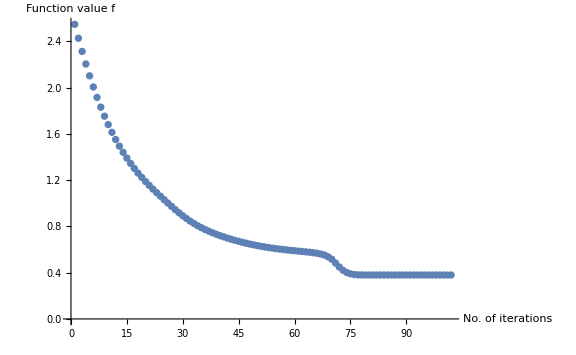

```mathematica
Print["Final value: ",Result[[1]]];
Print["Number of iterations: ",Result[[4]]//Total];
Print["Number of total corrections: ",Result[[3]]//Total];
ListPlot[Result[[4]], ImageSize->Large, AxesLabel->{"No. of iterations","Function value f"}]
```